# Lecture 17 - The Secrets we have Swept Under the Rug

Today’s lectures examines some of the quirky features of electrostatics that we have neglected up until this point

### A Puzzle...

Let’s go back to the basics and consider a point charge q at the origin. We can apply Gauss’s Law over a sphere of radius r centered at q to confirm that the radial electric field E⃗=E[r]r̂ satisfies q/ϵ_0=∫E⃗·ⅆ a⃗=4π r^2 E[r] and hence E⃗=q/(4π ϵ_0 r^2)r̂, as expected. However, using the divergence theorem, we could rewrite this integral over the surface of our sphere as the volume integral over the interior of the sphere (essentially switching between the integral and differential form of Gauss’s Law),

q/ϵ_0=∫(OverVector[∇]·E⃗)ⅆv

The divergence of the vector A⃗=A_r r̂+A_θ θ̂+A_ϕ ϕ̂ in spherical coordinates is given by OverVector[∇]·A⃗=1/r^2(∂[r^2 A_r])/(∂r)+1/(r Sin[θ])(∂[A_θ Sin[θ]])/(∂θ)+1/(r Sin[θ])(∂A_ϕ)/(∂ϕ). But when we evaluate the divergence for the point charge’s electric field E⃗=q/(4π ϵ_0 r^2)r̂, we get OverVector[∇]·E⃗=0, implying that the right-hand side of Equation (TextNumbered) equals zero instead of q/ϵ_0. Explain what is going on?

Solution
This problems highlights the subtly inherent in dealing with point charges, which are inherently strange objects. For example, the electric field infinitely close to a point charge diverges, and the energy required to make a point charge (which can be determined by integrating ϵ_0/2∫E^2 ⅆv over all space) similarly blows up. In this problem, we note that OverVector[∇]·E⃗=0 everywhere in space

...or rather, almost everywhere in space. The differential form of Gauss’s Law states that OverVector[∇]·E⃗=ρ/ϵ_0, and because the only charge is a point charge at the origin, it makes sense that OverVector[∇]·E⃗=0 at all other points in space. Indeed, if we consider any small closed Gaussian surface at any point in space that does not contain the origin, we expect that all electric field lines entering it will also leave it, implying that there is no net flux through the surface and that OverVector[∇]·E⃗=0.

But at the origin, something special happens. At this point, we know that OverVector[∇]·E⃗=ρ/ϵ_0, but what is ρ (the charge per unit volume)? The charge density of a point charge is infinite, since any box that surrounds the point charge, regardless of how small it is, will contain net charge q, so ρ diverges at the origin. It turns out that ρ blows up as a delta function (4π δ^3[r⃗]) which you will learn about in junior-level electrodynamics in a way that precisely implies that when you integrate ∫(OverVector[∇]·E⃗)ⅆv over any volume that contains the origin, no matter how small, the right-hand side of Equation (TextNumbered) will correctly evaluate to q/ϵ_0. □

### Some Interesting Mathematics

#### Non-Symmetric Gauss’s Law

Example
Consider the cross section of three infinite sheets intersecting at equal angles. The sheets all have surface charge density σ.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

1. By adding up the fields from the sheets, find the electric field at all points in space.
2. Find the field instead by using Gauss’s law. You should explain clearly why Gauss’s law is in fact useful in this setup.
3. What is the field in the analogous setup where there are N sheets instead of three? What is your answer in the N→∞ limit?

Solution
1. The electric field form a given sheet points away from the sheet and has uniform magnitude σ/(2 ϵ_0). Therefore, in any of the 6 regions of space divided by the sheets, the electric field at every point in this region will be the same. Considering a point on the x-axis (i.e. directly to the right of the intersection point in the diagram above), the electric field from the nearest two sheets will be 2 σ/(2 ϵ_0)Sin[π/3]=σ/(2 ϵ_0) in the x-direction. The contribution of the third sheet will also be σ/(2 ϵ_0) in the x-direction, leading to an electric field in this entire region of σ/ϵ_0 in the x-direction. By radial symmetry, this is the magnitude of the electric field in all of the regions, with the direction of it appropriately rotated in each region.

2. We use for our Gaussian surface a regular hexagon centered on the intersection point of the sheet.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Assume that the length of the Gaussian surface between two sheets is l and that its depth (going into and our of the page) is d. Because the electric field points perpendicularly outwards against our Gaussian surface, Gauss’s Law yields

E (6 l d)=((6 l d)σ)/ϵ_0

or equivalently E=σ/ϵ_0, as found above. Note that while Gauss’s Law is always valid, it is only useful when you can find a simple surface that is everywhere perpendicular to the electric field and where the electric field has a uniform value.

3. For general N, we use Gauss’s Law (or, for the mathematically minded, set up a summation over pairs of electric sheets as we did in the first part of this problem) using a regular 2N-gon with side length l and depth d. The surface area of this 2N-gon is (2N)(2 Sin[π/(2N)])l d and the charge enclosed is (2N)l d σ. So Gauss’s Law yields

E (2N l d)=(σ(2N)d)/ϵ_0 l/(2Sin[π/(2N)])

or equivalently E=σ/(2 ϵ_0 Sin[π/(2N)]). As expected, this is independent of l. And it agrees with the above result when N=3. For large N, Sin[π/(2N)]≈π/(2N) so E≈N/π σ/ϵ_0. In the case of large N, the sheets are very close to each other, so we effectively have a continuous volume charge distribution that depends on r. The separation between adjacent sheets grows linearly with r, so we have ρ[r]∝1/r. More precisely, you can easily show that ρ[r]=(N σ)/(π r). As a simple exercise, you can use Gauss’s Law to easily show that for a volume charge distribution with cylindrical symmetry and a constant electric field that is independent of r, we must have ρ[r]∝1/r. □

#### Electric Field at Corners

Example
1. Consider an thin sheet of uniform charge density σ (shown below) that extends infinitely in one direction and has a width b the other direction. What is the electric field at a distance x from the sheet? What happens as x→0?
2. A very long tube has a square cross section and uniform charge density σ. What will be the electric field at a corner? What is the electric field if the tube is a conductor so that the charge is free to flow?

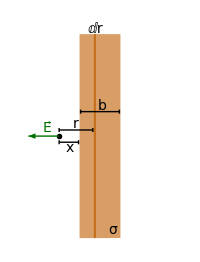

```mathematica
centerPlot@Graphics[{{PointSize[0.02],Point[{-2,0}]},{Lighter@color3,Rectangle[{-1,-5},{1,5}]},{color3,Rectangle[{-0.3,-5},{-0.2,5}]},{Darker@Darker@Green,Thick,Arrowheads[Medium],Arrow[{{-2,0},{-3.5,0}}],Text[font["E⃗"],{-2.6,0.4}]},{Line[{{{-2,-0.2},{-2,-0.4}},{{-2,-0.3},{-1.05,-0.3}},{{-1.05,-0.2},{-1.05,-0.4}}}],Text[font["x",Italic],{-1.5,-0.6}],Line[{{{-2,0.2},{-2,0.4}},{{-2,0.3},{-0.35,0.3}},{{-0.35,0.2},{-0.35,0.4}}}],Text[font["r",Italic],{-1.175,0.6}],Line[Map[{0,0.3}+#&,{{{-0.95,0.8},{-0.95,1.0}},{{-0.95,0.9},{0.95,0.9}},{{0.95,0.8},{0.95,1.0}}},{2}]],Text[font["b",Italic],{0.1,1.5}],Text[font["ⅆr"],{-0.25,5.25}]},Text[font["σ"],{0.6,-4.6}]},PlotRange->{{-4,4},{-5,5.5}},ImageSize->200]
```

Solution
Let’s start with a brief survey of the second part of the question, that is, of the electric field at the corner of a conducting tube. By symmetry, we know that the electric field must point diagonally away from the central axis of the tube. But this is problematic, since the electric field must point away from the surface of a conductor, and at the corner it seems that the electric field must point in two directions at once (to be normal to both faces it is touching). Your physics senses should be tingling.

```mathematica
centerPlot@Graphics3D[{{PointSize[0.04],Point[{0,-1,1}]},Cuboid[{-5,-1,-1},{5,1,1}],{Darker@Darker@Green,Thick,Arrow[{{0,-1,1},1.1{0,-2,2}}]}},Boxed->False,ImageSize->0.7{360.67825866064425,250.2343191851891},ImageSizeRaw->Automatic,ViewAngle->0.14688761695147076,ViewCenter->{{0.5,0.5,0.5},{0.32832817335899667,0.6358692135173696}},ViewPoint->{2.9464290295575997,-1.4973028227878877,0.7256998213115979},ViewVertical->{0.37417098968582096,-0.5213544832318052,3.0469167033263163}]
```

-Graphics3D-

1. To get a handle on the problem, let’s first consider the electric field from just one face of the conducting tube, or equivalently from an infinite conducting strip. Let’s assume for now that the strip has a uniform surface charge density σ, total width b and negligible thickness as shown above.

Treating each of the narrow strips as thin rods whose electric field (you will recall from Gauss’s Law) equals (E⃗)_rod=λ/(2π ϵ_0 r)r̂, the total electric field at a distance x from the side of the strip is given by

E⃗=∫_x^(x+b) σⅆr/(2π ϵ_0 r)=σ/(2π ϵ_0)Log[(x+b)/x]

As x→0, this result diverges (slowly, like Log[x]), and hence the electric field at the corner is infinite.

2. Now let’s turn to the full problem of a conducting tube. For the moment, we will assume that the tube has a constant charge density. From above, we know that the electric field at the corner must diverge due to the two faces that the point touches. The electric field from the other two faces is finite and also points in this same direction. Therefore, the electric field at the diverges at the corner of the tube.

Next, let us turn to a conducting tube and relax the assumption that the charge density σ as constant. In a conducting tube, the density would increase near the corners because of the self-repulsion of the charges. This has the effect of making the field even larger than the above reasoning would imply, so the above conclusion of a diverging field is still valid. In other words, this conclusion is true for both a conducting and nonconducting tube.

More generally, this type of divergence happens at any corner. For example, if you place a charge Q on a conducting cube, the electric field will diverge at the corners. As you can show, the divergence found above for the infinite strip does not occur as x→0 because the rods were infinitely long, but rather because of the bits of charge right on the edge of the strip, which will come infinitely close to our point of interest as x→0. This divergence occurs even when the angle at the corner is not 90° - it would also be true for a polygon with 100 sides, in which the surface bends by only a few degrees at each corner. This divergence also happens at a kink in a wire. □

#### Conducting Disk

Example
There is a very sneaky way of finding the charge distribution on a conducting circular disk with radius R and charge Q. Our goal is to find a charge distribution such that the electric field at any point in the disk has zero component parallel to the disk.

Recall from Problem 1.17 in the textbook (which you did in Homework 5) that the field at any point P inside a spherical shell with uniform surface charge density is zero, since the contributions due to both cones emerging from P cancel.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Consider the projection of this shell onto the equatorial plane containing P. Explain why this setup is relevant, and use it to find the desired charge density on a conducting disk.

Solution
Recall the argument in Problem 1.17 that showed why the field inside a spherical shell is zero. In the figure below, the two cones that define the charges q_1 and q_2 on the surface of the shell are similar, so the areas of the end patches are in the ratio of (r_1/r_2)^2. This factor exactly cancels the 1/r^2 effect in Coulomb’s law, so the fields from the two patches are equal and opposite at point P. The field contributions from the entire shell therefore cancel in pairs.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Now project the charges residing on the upper and lower hemispheres onto the equatorial plane containing P. The charges q_1 and q_2 in the patches mentioned above end up in the shaded patches shown in the figure above. The (horizontal) fields at point P from these shaded patches have magnitudes (k q_1)/x_1^2 and (k q_2)/x_2^2. But due to the similar triangles in the figure, x_1 and x_2 are in the same ratio as r_1 and r_2. Hence the two forces have equal magnitudes, just as they did in the case of the spherical shell. The forces from all of the various parts of the disk therefore again cancel in pairs, so the horizontal field is zero at P. Since P was arbitrary, we see that the horizontal field is zero everywhere in the disk formed by the projection of the charge from the original shell. We have therefore accomplished our goal of finding a charge distribution that produces zero electric field component parallel to the disk.

Since the spherical shell has a larger slope near the sides, more charge is above a given point in the equatorial plane near the edge, compared with at the center. The density of the conducting disk therefore grows with r, as shown in the figure below.

```mathematica
a=-Graphics-;
s1=0.001;
b=Show[Graphics3D[{{Opacity[0.5],Sphere[]},{Orange,Cylinder[{{0,0,-s1},{0,0,s1}}]},{Thickness[Medium],Line[{{{0,0,2s1},{0.69,0,2s1}},{{0,0,0},{0,0,1}},{{0,0,0},{Sin[1.95π/8],0,Cos[1.95π/8]}}}](*,Text[font["r",Italic,16]]*)}}],ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,1.9π/8,2π/8},{ϕ,0,2π},PlotPoints->100,Mesh->None,PlotStyle->RGBColor[0.28, 0.29, 1]],ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],5s1},{θ,1.9π/8,2π/8},{ϕ,0,2π},PlotPoints->50,Mesh->None,PlotStyle->RGBColor[0.28, 0.29, 1]],Boxed->False,ImageSize->140{1,1},ViewAngle->0.29553175426564016,ViewCenter->{{0.5,0.5,0.5},{0.5058277574147878,0.506337738717115}},ViewPoint->{0.1309353876223835,-3.26858210208004,0.86557897746549}];
centerPlot@Grid[{{a,b}},Spacings->5]
```

-Graphics- | -Graphics3D-

To be quantitative, we want to find the charge density σ_disk[r] when we collapse the sphere with uniform charge density σ_sphere onto the disk. The charge on an infinitesimal patch of the disk a given point (r,ϕ) will be σ_disk[r](r ⅆrⅆϕ). Using the diagram above, the patch on the sphere above the point (r,ϕ) will have length ⅆr/Cos[θ], width rⅆϕ, and therefore a total charge of 2σ_sphere(rⅆϕ)(ⅆr/Cos[θ]). Note that the factor of 2 emerges since we collapse both this patch and its symmetric counterpart at θ→π-θ. Equating these two charges, we find

σ_disk[r]=(2 σ_sphere)/Cos[θ]

To remove the Cos[θ], we note that r=R Sin[θ] so that Cos[θ]=(1-(r/R)^2)^(1/2), and hence

σ_disk[r]=(2 σ_sphere)/((1-(r/R)^2)^(1/2))

As a double check, we can use σ_sphere=Q/(4π R^2) and ensure that the total charge on the disk will be Q,

∫_0^(2π) ∫_0^R (2 σ_sphere)/((1-(r/R)^2)^(1/2))rⅆrⅆϕ=4π σ_sphere∫_0^R r/((1-(r/R)^2)^(1/2))ⅆr
=4π σ_sphere{-(R^2(1-(r/R)^2))^(1/2)}_(r=0)^(r=R)
=4π σ_sphere R^2
=Q

The density diverges at the edge of the conducting disk, but the total charge has the finite value Q. It is fairly intuitive that the density should grow as r increases, because charges repel each other toward the edge of the disk. However, one should be careful with this type of reasoning. In the lower-dimensional analog involving a one-dimensional rod of charge, the density is actually essentially uniform, all the way out to the end; see the next problem. □

#### Conducting Stick

Example
The same strategy from the previous problem can be used to find the charge distribution on a conducting stick. Consider a stick of length 2R centered at the origin and lying on the x-axis. To find the charge λ[x]ⅆx which lies between x and x+ⅆx on the stick, consider a sphere of radius R centered at the origin. Collapse all of the charge between x and x+ⅆx onto the x-axis, and find the charge distribution λ[x] of the conducting stick. Then explain why this answer is absolutely absurd (and yet still correct!).

Solution
We follow the same strategy as for the Conducting Disk, namely, to take a sphere of radius R and collapse it down onto a rod. We know that each patch on the two cones emerging from P will cancel each other, and this cancellation continues after we project the two patches onto the x-axis (see below, left). Therefore, the charge λ[x]ⅆx between x and x+ⅆx on the rod will be given by the total charge on the ring of the charged sphere between x and x+ⅆx (below, right).

```mathematica
a=-Graphics-;
s1=0.001;s2=0.02;
b=Show[Graphics3D[{{Opacity[0.5],Sphere[]},{Orange,Cylinder[{{0,0,-1},{0,0,1}},s2]},{Thickness[Medium],Line[{{{0,0,2s1},{-1,0,2s1}},{{0,0,0},{-Sin[1.95π/8],0,Cos[1.95π/8]}}}],Dashed,Line[{{-Sin[1.95π/8],0,Cos[1.95π/8]},{0,0,Cos[1.95π/8]}}]},Text[font["r",Italic,13],{0,0,Cos[1.95π/8]/2}+{0.1,0,0}],Text[font["R",Italic,13],{-0.5,0,-0.1}],Text[font["θ",12],{-0.18,0,0.07}]}],ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,1.9π/8,2π/8},{ϕ,0,2π},PlotPoints->100,Mesh->None,PlotStyle->RGBColor[0.28, 0.29, 1]],ParametricPlot3D[{1.1s2 Cos[ϕ],1.1s2 Sin[ϕ],Cos[θ]},{θ,1.9π/8,2π/8},{ϕ,0,2π},PlotPoints->50,Mesh->None,PlotStyle->RGBColor[0.28, 0.29, 1]],Boxed->False,ImageSize->140{1,1},ViewAngle->0.29553175426564016,ViewCenter->{{0.5,0.5,0.5},{0.5058277574147878,0.506337738717115}},ViewPoint->{-0.2390629503674264,-3.3596020120177283,-0.3254584867660643},ViewVertical->{-0.9823857924156832,-0.18601867064857633,-0.017754127124323664}];
centerPlot@Grid[{{a,b}},Spacings->5]
```

-Graphics- | -Graphics3D-

As we saw above for the Conducting Disk, the diagonal length of a ring at a distance x from the center of the sphere is ⅆx/Cos[θ], and the circumference of this ring (which has radius (R^2-x^2)^(1/2)) is 2π (R^2-x^2)^(1/2). Since x=R Sin[θ], Cos[θ]=(1-(x/R)^2)^(1/2) so that the total charge on this ring is given by

λ[x]ⅆx=2π (σ_sphere(R^2-x^2))^(1/2)ⅆx/((1-(x/R)^2)^(1/2))=2π R σ_sphere ⅆx

As a quick double check, the full charge over the entire sphere assuming σ_sphere=Q/(4π R^2) is

∫_-R^R λ[x]ⅆx=4π R^2 σ_sphere=Q

as expected. Equation (TextNumbered) implies that the charge density on a conducting rod is

λ[x]=2π R σ_sphere=Q/(2R)

Shockingly, this is uniform! This is an absolutely astonishing result!!!

In case your jaw isn’t hanging open, consider how unintuitive this result is. A point at the center of a uniformly charged rod will certainly feel zero force by symmetry, but any point not in the exact center will feel a force pointing away from the center there will be more charged rod on one of its sides than the other. As a particularly troublesome case, consider the force on the very ends of the rod - clearly these must point outwards. So how can this charge density be correct?

As a fun historical aside, there was a very lively debate over the charge density of a conducting stick. Part of the problem was the apparently ridiculous nature of the uniform charge density solution. Another issue is that the charge density on a conducting needle seemed to be different depending on which model you use (see Charge on a Conducting Needle by Griffiths and Li 1996 for an excellent discussion of this problem).

This problem is discussed extensively in Problem 3.5 of the textbook. Loosely speaking, it turns out that if you correct the uniform charge density by breaking up the stick into N small segments and letting all of the segments (except the two end segments) move to their equilibrium positions, then in the limit N→∞ the movement required by each segment will shrink to zero. In this limit, the two end segments can be ignored since they are single points on a 1D rod. You are invited to think about this perplexing problem and read over the fantastic description in the text. □

#### Image Charge of a Conducting Cylinder

Example
We covered the image charge scenario on an infinite grounded conducting sheet and on a grounded conducting sphere, but we never addressed the case of a grounded infinite cylinder.

1. Explain why the method of images cannot be used to find the electric field everywhere outside a grounded conducting cylinder of radius R when a point charge Q is brought next to the cylinder.

2. Nevertheless, the method of images can work in the proper setting for a grounded conducting cylinder. Consider a cylinder with radius R whose axis lies on the z-axis. A line of constant charge density λ, lying parallel to the z-axis, is placed at a distance A from the cylinder. Show that an image line with charge density -λ at a distance R^2/A from the center of the cylinder makes the cylinder an equipotential. If the cylinder is grounded, what further image charge is needed to find the potential outside the cylinder?
Hint: Recall that the potential from a line of charge has the form ϕ=λ/(2π ϵ_0)Log[r/r_0] where r_0 is a reference length at which we set the potential to be zero.

Solution
1. Recall what the image charge configuration was for a grounded conducting sphere:

```mathematica
centerPlot@-Graphics-
```

-Graphics-

If we take a cross section of the cylinder in the plane containing the charge Q, we will get this same picture. Label the center of the cylinder as (0,0,0), place the real charge at (A,0,0), and put the image charge at (R^2/A,0,0). If any image charge configuration will be possible for the cylinder, it will have to be this exactly same one shown for the sphere - an image charge -(Q R)/A at a distance R^2/A from the axis of the cylinder. Why?

Because the potential must be zero everywhere on the circular cross section of the cylinder shown, and we can show that the only way to make this true is with this image charge at this location. And indeed this cross section of the cylinder will be at zero potential. But what about the remainder of the cylinder? Consider the point (R,0,ϵ), which is ϵ deeper into the page than the point (R,0,0) on the cylinder that lies right between the real and image charge. The point (R,0,ϵ) is at a distance

({R-R^2/A}^2+ϵ^2)^(1/2)≈R/A(A-R)+1/(2(A-R))A/R ϵ^2+O[ϵ^4]

from the image charge and a distance

({A-R}^2+ϵ^2)^(1/2)≈(A-R)+1/(2(A-R))ϵ^2+O[ϵ^4]

```mathematica
FullSimplify[Series[((R-R^2/A)^2+ϵ^2)^(1/2),{ϵ,0,2}],0<R<A]
FullSimplify[Series[((A-R)^2+ϵ^2)^(1/2),{ϵ,0,2}],0<R<A]
```

((A-R) R)/A+(A ϵ^2)/(2 A R-2 R^2)+O[ϵ]^3

(A-R)+ϵ^2/(2 A-2 R)+O[ϵ]^3

from the real charge. Since A/R>1, the distance of the point (R,0,ϵ) from the image charge grows faster than the distance from the real charge, and hence the potential off the cross section of the cylinder shown will not be zero. In other words, no point image charge can accommodate the infinite grounded cylinder.

2. We will use cylindrical coordinates with the polar angle θ taken from the axis going through the real and image charges. Using the Law of Cosines, the potential everywhere on this cross section of the cylinder is given by

ϕ=λ/(2π ϵ_0)Log[((A^2+R^2-2A R Cos[θ])^(1/2))/r_0]-λ/(2π ϵ_0)Log[((R^4/A^2+R^2-2 R/A R Cos[θ])^(1/2))/r_0]
=λ/(2π ϵ_0)(Log[((A^2+R^2-2A R Cos[θ])^(1/2))/r_0]-Log[(R/A(A^2+R^2-2A R Cos[θ])^(1/2))/r_0])
=λ/(2π ϵ_0)Log[A/R]

Therefore, the image charge configuration proposed makes the cylinder an equipotential. If the cylinder is grounded, then we should add another line with charge density λ̃ right on the axis of the cylinder, which will add a potential (λ̃)/(2π ϵ_0)Log[R/r_0] everywhere on the cylinder. Hence, to make the potential of the cylinder zero, we must have

λ/(2π ϵ_0)Log[A/R]+(λ̃)/(2π ϵ_0)Log[R/r_0]=0

or equivalently

λ̃=-λ Log[A/R]/Log[R/r_0]

Note that what we are really asking here is for the potential everywhere on the grounded cylinder to have the same potential as a point at a distance r_0 from a line of charge. □

#### Maximum Field from a Blob

Example
1. A point charge is placed somewhere on the curve shown below. This point charge creates an electric field at the origin. Let E_y be the vertical component of this field.What shape (up to a scaling factor) should the curve take so that E_y is independent of the position of the point charge on the curve?
2. You have a moldable material with uniform volume charge density. What shape should the material take if you want to create the largest possible electric field at a given point in space?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
1. Label the points on the curve by their distance r from the origin and an angle θ from the line that this distance subtends with the y-axis.

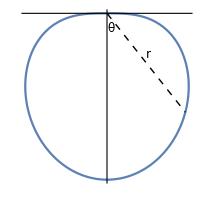

```mathematica
p1={1/2^(1/4)1/(√2),-1/2^(1/4)1/(√2)};
ft=12;
centerPlot@Show[PolarPlot[√Cos[θ+π/2],{θ,0,2π},Ticks->None],Graphics[{Dashed,Line[{{0,0},p1}],Text[Style["r",ft],p1/2+{0.02,0.05}],Text[Style["θ",ft],{0.03,-0.09}]}],ImageSize->200]
```

Then a point charge q on the curve provides a y component of the electric field at the origin equal to

E_y=(k q)/r^2 Cos[θ]

If we want for this to be independent of the charge’s location on the curve, then we must have r^2∝Cos[θ]. Therefore, the curve must have the form

r^2=c^2 Cos[θ]

or equivalently

r=c √Cos[θ]

for some constant c. (We have chosen the positive square root. The negative square root would also work, and it would yield the same curve reflected about the x-axis. Therefore, we only need one of these curves.) This yields a family of curves indexed by c. Note that we ignore the points at r=0 at θ=π/2 and θ=(3π)/2.

2. Assume that the material has been shaped and positioned so that the electric field at the origin takes on the maximum possible value. Assume that the field points in the y-direction. Then all the small elements of charge ⅆq on the surface of the material must give equal contributions to the y component of the field at the origin. This is true because if it weren’t the case, then we could simply move a tiny piece of the material from one point on the surface to another, thereby increasing the field at the origin and contradicting our assumption that the field at the origin is maximum. From Part 1, any vertical cross section (formed by the intersection of the surface with a plane containing the y-axis) must therefore look like the r=c √Cos[θ] curve we found. Equivalently, the desired shape of the material is obtained by forming the surface of revolution of the r=c √Cos[θ] curve about the y-axis with c taking the greatest possible value it can attain to use up all of the material. □

### Symmetry and Superposition

A final, dramatic skit to recap everything that we have learned!

It all began with Coulomb’s Law for a point charge. Of course, since the geometry of having a single point is symmetric, there must be radial symmetry in the electric field. E=(k q)/r^2 for a point charge, and in a sense that solves all of electricity for us because any charge distribution can then be understood by superposition

But, nevertheless, there are so many interesting cases where we can get beautiful analytic results. So then we busted out a series of neat tricks. First, there was Gauss’s Law, and as always, we started from a point charge. Because the electric field is ∝1/r^2, the flux through a sphere will be E (area)∝1/r^2(4π r^2) which does not depend on r. Believe it or not, this is an example of symmetry of the 1/r^2 nature of the electric field. And once you know Gauss’s Law for a point charge, you know it for any charge distribution by superposition.

So that really opened the door for us. A line of charge is radially symmetric and also translationally symmetric. And that is enough information to use Gauss’s law, and we found that the electric field of a line varies as 1/r with the radial distance. And then we considered the infinite sheet, which has both translational and rotational symmetry, and found that the electric field is constant everywhere in space. Of course, you can also think of an infinite sheet as a bunch of rods glued together, which really means to use superposition, and you recoup the same answer.

So then we took the next step and jumped to conductors. Here, the name of the game is to throw a certain quantity of charge on a conductor, and then that charge will rearrange itself so that the electric field will be zero inside and the conductor and perpendicular to the surface right outside the conductor. The uniqueness theorem tells us that if you find one solution, that is the only possible charge configuration. But nevertheless, we should not forget about our favorite tool of using symmetry. If there is symmetry in the geometry, this same symmetry will exist in the final charge distribution. Charge on an isolated spherical conductor will distribute symmetrically over the sphere. If your setup has reflection symmetry, the final charge distribution will have this same reflection symmetry.

Another cool trick with conductors is to use the method of images, which really just boils down to using the symmetry of different setups. The infinite plane has reflection symmetry, and hence its image charge is just a reflection. The sphere has an inversion symmetry which corresponds to its image charge. The cylinder also has its own reflection symmetry, and although we did not talk about it in class I added a problem about it in today’s notes

And finally, we graduated from electrostatics and moved into circuits. Shockingly enough, here the most important tool was superposition. Of course, you might not recognize it, since we rephrase everything in the language of circuits. Conservation of charge is translated into the current going into a junction equals the current coming out of the junction. ∮E⃗·ⅆ s⃗=0 is translated into the voltage across a loop equals zero. And the general principle of superposition is translated into currents are vectors which add together. It doesn’t sound very surprising when phrased in that way, but the fact that current is a vector is rather deep.

And we just got a hint, the merest brush, with changing currents when we talked about charging and discharging capacitors. And that is Ph 1b in a nutshell. And in Ph 1c, the first thing you will do is analyze what happens in the general setting when currents can increase or decrease. You will combine electricity together with special relativity, and it will be the most amazing lecture ever. You will literally be jumping out of your seats in class!

And with that, I would like to thank you very much for your attention and enthusiasm this term. I had a wonderful time teaching Ph 1b to you all, and I will hope to see many of you in my capacity as the Bi 1 TA next term! Good luck on finals!!!

## Mathematica Initialization

```mathematica
{color1,color2,color3}=ColorData[97][#]&/@{1,10,6};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered